Outline of what to do:
-Decompose a polyhedron into its vertices 
-Create a graph for those vertices
-Find the dual of the polyhedron
-Create a graph in the same way
-Generate a list of faces in 2D
-generate possible alignments of faces
-create a net by testing all possible positions

## Creating graphs for the polyhedron and its dual

```mathematica
ClearAll[polyhedrongraph]

polyhedrongraph[polyhedron_]:= 
Block[{vertexlist,vertexpairings,sortedvertices},

     vertexlist = polyhedron[[2]];
     
     vertexpairings = Flatten[
     Table[
     Append[
     Partition[vertexlist[[n]], 2, 1],
     {Last[vertexlist[[n]]],First[vertexlist[[n]]]}],
     {n, 1, Length[vertexlist]}], 
     1];
     
     sortedvertices = Sort /@ vertexpairings // DeleteDuplicates;


Graph[UndirectedEdge@@@sortedvertices,VertexLabels -> "Name"]
]
```

```mathematica
sunny = RandomPolyhedron[{"ConvexHull",30}]
sunnydual = DualPolyhedron[sunny]
```

Polyhedron[…]

Polyhedron[…]

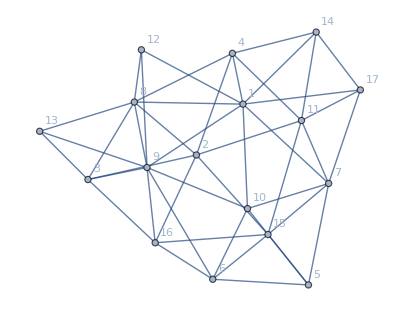
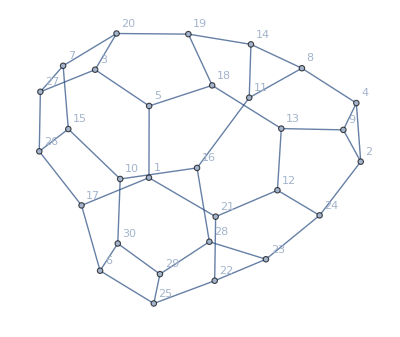
{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
{Graphics3D[sunny],polyhedrongraph[sunny],Graphics3D[sunnydual],polyhedrongraph[sunnydual]}
```

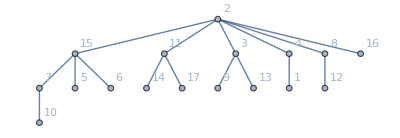
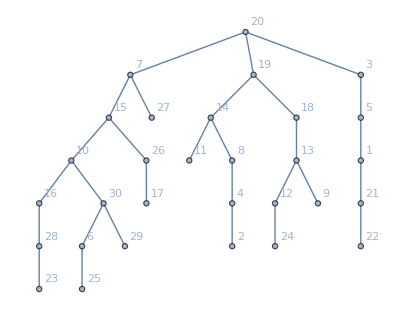

```mathematica
{FindSpanningTree[polyhedrongraph[sunny]],FindSpanningTree[polyhedrongraph[sunnydual]]}
```

# Generating faces

```mathematica
normvector[coords_] :=
Cross[coords[[2]]-coords[[1]],coords[[3]]-coords[[1]]];

transform[n_] := 
N@RotationTransform[{normvector[coordinategroups[[n]]],{0,0,-1}},Mean[coordinategroups[[n]]]];


extractfaces[polyhedron_] :=
Block[{coordinatelist,vertexlist,transformedvertices,polygoncoords},

coordinatelist = polyhedron[[1]];
vertexlist = polyhedron[[2]];

transformedvertices = Table[transform[n]@coordinategroups[[n]],{n,1,Length[coordinategroups]}];

polygoncoords = Table[Delete[transformedvertices[[n,m]],{3}],{n,1,Length[transformedvertices]},{m,1,3}];

Table[Graphics[Polygon[polygoncoords[[n]]]],{n,1,Length[polygoncoords]}]

]
```

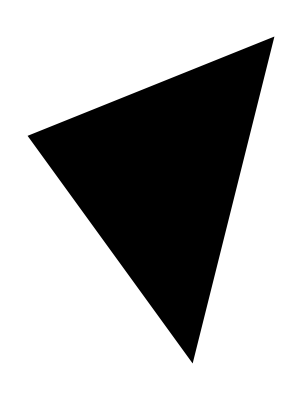
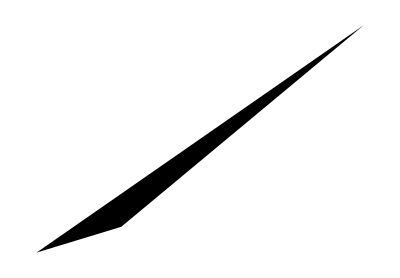
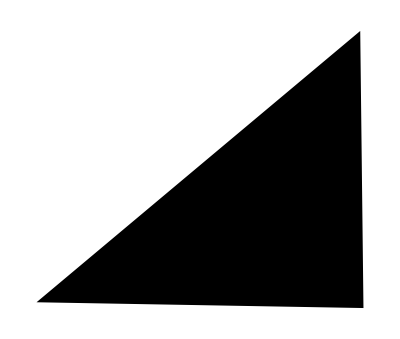
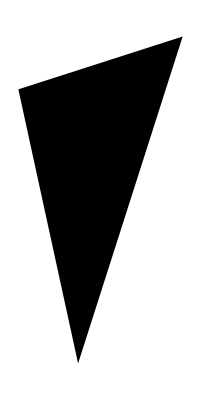
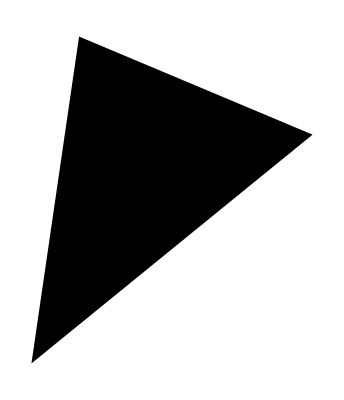
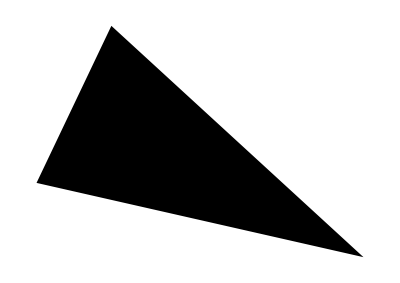
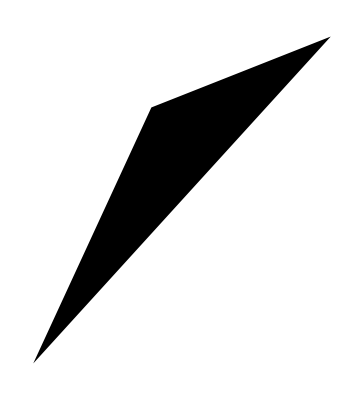
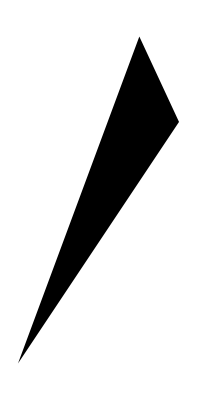

```mathematica
extractfaces[sunny]
```

# Associations and nets

```mathematica
coordinatelist = sunny[[1]];
vassoc = Merge[Join@Table[<|n -> coordinatelist[[n ]]|>,{n,1,Length[coordinatelist]}],Total];
edgeassoc =Merge[Join@Table[<|n -> EdgeList[polyhedrongraph@sunny][[n ]]|>,{n,1,Length[EdgeList[polyhedrongraph@sunny]]}],Total];
facepath=Partition[FindShortestTour[polyhedrongraph[sunnydual]][[2]], 2, 1];

vertexlist = sunny[[2]];

MeshPrimitives[BoundaryDiscretizeGraphics@sunny,2];

coordinategroups = Table[vassoc/@vertexlist[[n]],{n, 1, Length[vertexlist]}];

table = Table[Subsets[coordinategroups[[n]],{2}],{n,1,Length[coordinategroups]}];
```

```mathematica
coordinatelist
```

{{0.99775,0.460658,0.87073},{0.606058,0.203199,0.0441917},{0.734397,0.947459,0.260964},{0.970841,0.312109,0.384182},{0.0173335,0.730968,0.70973},{0.0572779,0.971757,0.479634},{0.0481243,0.349352,0.940989},{0.972582,0.366209,0.265801},{0.902352,0.95113,0.692814},{0.0855349,0.632285,0.864048},{0.326339,0.0765102,0.633665},{0.964226,0.766745,0.720768},{0.792157,0.927409,0.343825},{0.822383,0.256237,0.836316},{0.101975,0.0794383,0.126185},{0.25429,0.976916,0.126518},{0.44426,0.183767,0.930738}}